Units used: GeV for masses, ps for lifetimes, cm for distances

```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookSave[];
```

```mathematica
SetDirectory[ NotebookDirectory[]]
```

/home/stasya/prj/B-K

### Plotting stuff

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
```

```mathematica
ColorScheme="SolarColors";
```

```mathematica
PlotContours[f_,BR_,mmin_,mmax_,αmin_,αmax_,cmin_,cmax_,Nlabeles_]:=Style[ContourPlot[f[mϕ,α,BR],{mϕ,mmin,mmax},{α,αmin,αmax},FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},PlotRange-> Full,Contours->{10^-12,10^-11,10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,10^-3},Exclusions->None,ColorFunctionScaling->False,ColorFunction->(ColorData[ColorScheme][LogarithmicScaling[#,cmin,cmax]]&)
  ,PlotLegends->BarLegend[{ColorData[ColorScheme],{0,1}},LegendMarkerSize->470,Ticks->({LogarithmicScaling[#,cmin,cmax],ScientificForm[#//N,2]}&/@(cmin (cmax/cmin)^Range[0,1,1/Nlabeles]))],ImageSize-> 500],AutoStyleOptions->{"HighlightFormattingErrors"->False}]
```

```mathematica
PlotContoursLabeled[f_,BR_,mmin_,mmax_,αmin_,αmax_,cmin_,cmax_,Nlabeles_,labelsmϕpos_]:=
Module[{lblXY,contours},
contours=PowerRange[cmin,cmax];
(*lblXY=({labelsmϕpos,ScientificForm[#//N,2]}&/@(10^-5(10^-2/10^-5)^Range[0,1,1/Nlabeles]));*)
lblXY=({labelsmϕpos,ScientificForm[#//N,2]}&/@(10^-2(1)^Range[0,1,1/Nlabeles]));
Print[contours//N];
Print[lblXY];

Style[ContourPlot[f[mϕ,α,BR],{mϕ,mmin,mmax},{α,αmin,αmax},FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},PlotRange-> Full,Contours->contours,Exclusions->None,ColorFunctionScaling->False,ColorFunction->(ColorData[ColorScheme][LogarithmicScaling[#,cmin,cmax]]&)
  ,PlotLegends->BarLegend[{ColorData[ColorScheme],{0,1}},LegendMarkerSize->470,Ticks->({LogarithmicScaling[#,cmin,cmax],ScientificForm[#//N,2]}&/@(cmin (cmax/cmin)^Range[0,1,1/Nlabeles]))],ImageSize-> 500,Epilog->{Thread[Text[contours//N,lblXY,Background->White]]}],AutoStyleOptions->{"HighlightFormattingErrors"->False}]]
```

```mathematica
({0.25,ScientificForm[#//N,2]}&/@(10^-5(10^-2/10^-5)^Range[0,1,1/8]))
```

{{0.25,1.×10^-5},{0.25,2.4×10^-5},{0.25,5.6×10^-5},{0.25,1.3×10^-4},{0.25,3.2×10^-4},{0.25,7.5×10^-4},{0.25,1.8×10^-3},{0.25,4.2×10^-3},{0.25,1.×10^-2}}

### Belle II parameters

```mathematica
τB=1.638;(*ps*)
ΓtotalB=6.582*10^-25/(10^-12 τB);(*GeV*)
cτB=3 10^10 10^-12 τB(*in cm*);
```

```mathematica
Belle2params={γβB:>0.248,RKLM:>300,θKLMMin:>40 Degree, θKLMMax:>129 Degree,RCDC:>162,θCDCMin:>17 Degree, θCDCMax:>150 Degree};
```

### Init

```mathematica
tplus=(mB+mK)^2;
tminus=(mB-mK)^2;
tzero=tplus(1-Sqrt[1-tminus/tplus]);
```

```mathematica
z[t_]=(Sqrt[tplus-t]-Sqrt[tplus-tzero])/(Sqrt[tplus-t]+Sqrt[tplus-tzero]);
```

```mathematica
F[q.b2_,x_]=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](z[q.b2]-z[0])^k,{k,0,2}]//Simplify;
```

```mathematica
formFactors={fplus[q.b2_]:> F[q.b2,fplus], fzero[q.b2_]:> F[q.b2,fzero]};
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 };
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,MB:>4.18,mb:>4.18,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MT:>173,mt:>173,MS:>0.095,ms:>0.095,mB:>5.279,mK:>0.4937,mπ:>0.14,mD:>1.86,v:>246,me:>0.000511,mμ:>0.106,mτ:>1.777,MD:>0.0047,md:>0.0047,Γh:>0.013,mBs:>5.367,fBs:>0.227,mBd:>5.280,fBd:>0.188,vev:>246.22};
ckms={CKM[3,3]:>0.999,Vtb:>0.999,CKM[3,2]:>0.0404,Vts:>0.0404,CKM[2,3]:>0.0412,Vcb:>0.0412,CKM[2,2]:>0.973,Vcs:>0.973, Vtd:> 8.1/1000};
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181,Subscript[X,t]:>1.469,sw.b2:>0.231};
eulergamma={Subscript[γ,E]:>0.5772};
```

### Γϕ

```mathematica
datapointsππ=ReadList[File["rate_pipi.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

```mathematica
datapointsππ={{0.28001323,5.17024*10^(-10)},{0.27784854,1.0525554*10^(-9)},{0.2877911,1.8218304*10^(-9)},{0.30592537,3.3623317*10^(-9)},{0.33365947,5.277515*10^(-9)},{0.3639078,8.283586*10^(-9)},{0.41079497,1.2181233*10^(-8)},{0.47179008,1.7907567*10^(-8)},{0.5560635,2.7178222*10^(-8)},{0.6442094,4.2615103*10^(-8)},{0.73974603,5.5053757*10^(-8)},{0.8280175,9.213942*10^(-8)},{0.8877805,1.6462049*10^(-7)},{0.9437583,3.1379568*10^(-7)},{0.97783643,7.033213*10^(-7)},{1.002676,3.6842826*10^(-7)},{1.036807,1.5896644*10^(-7)},{1.0629779,7.317836*10^(-8)},{1.108985,3.958082*10^(-8)},{1.1371115,2.0074902*10^(-8)},{1.1865596,1.27616815*10^(-8)},{1.2277195,9.23311*10^(-9)},{1.2817607,8.933028*10^(-9)},{1.3385478,1.08358424*10^(-8)},{1.3852515,9.2141486*10^(-9)},{1.47,4.38*10^(-9)},{1.5,2.5269602*10^(-9)},{1.5614661,4.1001567*10^(-9)},{1.6033295,6.6537464*10^(-9)},{1.6742321,7.566051*10^(-9)},{1.7473112,5.4732547*10^(-9)},{1.8077103,3.5941348*10^(-9)},{1.88713,3.25975*10^(-9)},{1.9999999,3.7056085*10^(-9)}};
```

```mathematica
Γϕππ=Interpolation[datapointsππ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
datapointsKK=ReadList[File["rate_KK.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

```mathematica
datapointsKK={{0.992899,1.39798*10^(-7)},{1.07269,1.07816*10^(-7)},{1.13916,8.87269*10^(-8)},{1.25236,8.04012*10^(-8)},{1.31897,8.56912*10^(-8)},{1.45009,8.02007*10^(-8)},{1.58049,7.26857*10^(-8)}{1.69277,5.42831*10^(-8)},{1.81310,4.18707*10^(-8)},{1.99304,3.44371*10^(-8)}};
```

```mathematica
ΓϕKK=Interpolation[datapointsKK,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.250016} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.265991} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.282986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

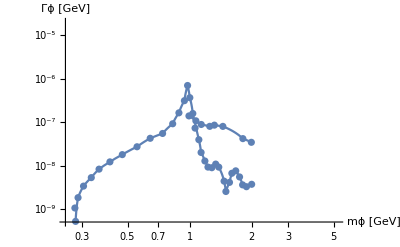

```mathematica
Show[LogLogPlot[{ΓϕKK[mϕ]*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ]},{mϕ,0.25,5.2},PlotRange->{{0.25,5.2},{5*10^(-10),2*10^(-5)}},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],ListPlot[datapointsKK,PlotRange->{5*10^(-10),2*10^(-5)},ScalingFunctions->{"Log","Log"},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],LogLogPlot[Γϕππ[mϕ]*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ],{mϕ,0.25,5.2},PlotRange->{5*10^(-10),2*10^(-5)},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],ListPlot[datapointsππ,PlotRange->{5*10^(-10),2*10^(-5)},ScalingFunctions->{"Log","Log"},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}]]
```

```mathematica
alphaSValues={{1.03,0.49},{1.27,0.40},{1.55,0.34},{2.14,0.28},{3.48,0.23},{6.11,0.19}};
```

```mathematica
AlphaS=Interpolation[alphaSValues,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2) (* dark fermion *)
Γϕf[mϕ_,α_,mf_]:=HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2))/(8 π mϕ^2) (* lepton *)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* W-boson *)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* Z-boson*)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2) (* Photon *)
Γϕg[mϕ_,α_]:=(Sin[α]^2alphas^2mϕ^3)/(32π^3 v^2) Abs[Sum[((mϕ^2/(4mq^2))+((mϕ^2/(4mq^2))-1)*(HeavisideTheta[(mϕ^2/(4mq^2))-1]*(-1/4) (Log[(1+Sqrt[1-1/(mϕ^2/(4mq^2))])/(1-Sqrt[1-1/(mϕ^2/(4mq^2))])]-I π)^2+HeavisideTheta[-(mϕ^2/(4mq^2))+1]ArcSin[Sqrt[(mϕ^2/(4mq^2))]]^2))/((mϕ^2/(4mq^2))^2),{mq,{mu,md,ms,mc,mb,mt}}]]^2*HeavisideTheta[mϕ-2](* gluons *)
Γϕπ[mϕ_,α_]:= Γϕππ[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ] (* pion *)
ΓϕK[mϕ_,α_]:= ΓϕKK[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ] (* kaon *)
Γϕs[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mK] ((ms/v)^2 Sin[α]^2 (mϕ^2-4 mK^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* strange quarks *)
Γϕc[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mD] ((mc/v)^2 Sin[α]^2 (mϕ^2-4 mD^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* charm quarks *)
Γϕb[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mB] ((mb/v)^2 Sin[α]^2 (mϕ^2-4 mB^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* bottom quarks *)
Γϕmoreπs[mϕ_,α_]:=5.1*10^(-9) Sin[α]^2 mϕ^2 Sqrt[mϕ^2-4mπ^2]*HeavisideTheta[mϕ-4mπ]*HeavisideTheta[2-mϕ] (* additional meson contributions *)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α,me]+Γϕf[mϕ,α,mμ]+Γϕf[mϕ,α,mτ]+Γϕπ[mϕ,α]+ΓϕK[mϕ,α]+Γϕmoreπs[mϕ,α]+Γϕg[mϕ,α]+Γϕs[mϕ,α]+Γϕc[mϕ,α]+Γϕb[mϕ,α]+Γϕγ[mϕ,α]+ΓϕW[mϕ,α]+ΓϕZ[mϕ,α])/.{alphas:>AlphaS[mϕ]}/.masses/.couplings
ΓϕSM[mϕ_,α_]:=Γϕ[mϕ,mϕ,0,α]
ΓϕBRDM[mϕ_,α_,BRχ_]:=ΓϕSM[mϕ,α](1+BRχ/(1-BRχ))(*ΓSM+Γχ for given BRχ*)
τϕ[mϕ_,mχ_,ξ_,α_]:=10^12(Γϕ[mϕ,mχ,ξ,α] GevToInverseSec)^-1/.constants (*in psc*)
τϕBRDM[mϕ_,α_,BRχ_]:=10^12(ΓϕBRDM[mϕ,α,BRχ] GevToInverseSec)^-1/.constants (*in psc*)
cτϕBRDM[mϕ_,α_,BRχ_]:=3 10^10 10^-12 τϕBRDM[mϕ,α,BRχ](*in cm*)
cτϕVisible[mϕ_,α_]:=3 10^10(ΓϕSM[mϕ,α] GevToInverseSec)^-1/.constants (*in psc*)
Γϕtoμμ[mϕ_,α_]:=HeavisideTheta[mϕ-2 mμ] ((mμ/v)^2 Sin[α]^2 (mϕ^2-4 mμ^2)^(3/2))/(8 π mϕ^2)
```

```mathematica
τϕ[1,1,0,0.1]-τϕBRDM[1,0.1,0]
```

0.+0. ⅈ

### Geometrical integration over detector

```mathematica
γβ[γβParent_,mParent_,mϕ_]:=γβParent mParent/(2 mϕ)/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
θminBoost[θmin_,r_,cτ_,γβ_]:=ArcTan[r/(r/Tan[θmin]-γβ cτ)]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
θmaxBoost[θmax_,r_,cτ_,γβ_]:=π+ArcTan[-r/(-r/Tan[θmax]+γβ cτ)]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
GeomInt[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=NIntegrate[Sin[θ]/2(ⅇ^(-dmin/(Sin[θ] γβ  cτ))-ⅇ^(-dmax/(Sin[θ] γβ cτ)))/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{θ,θmin,θmax}]
```

```mathematica
GeomIntInvisible[θmin_,θmax_,dmin_,cτ_,γβ_]:=NIntegrate[Sin[θ]/2 ⅇ^(-dmin/(Sin[θ] γβ  cτ))/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{θ,θmin,θmax}]
```

B decays

### Geometry

```mathematica
γβϕB[mϕ_]:=γβ[γβB,mB,mϕ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
(*Integrations with requirebments that B decays within Belle2*)
```

```mathematica
GeomIntBelleII[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=HeavisideTheta[Re[RKLM/Tan[θmin]-γβB cτB]]GeomInt[θmin,θmax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
GeomIntBelleIICDC[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=HeavisideTheta[Re[RCDC/Tan[θmin]-γβB cτB]]GeomInt[θmin,θmax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
GeomIntInvBelleII[θmin_,θmax_,dmin_,cτ_,γβ_]:=HeavisideTheta[Re[RKLM/Tan[θmin]-γβB cτB]]GeomIntInvisible[θmin,θmax,dmin,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
GeomIntInvBelleIICDC[θmin_,θmax_,dmin_,cτ_,γβ_]:=HeavisideTheta[Re[RCDC/Tan[θmin]-γβB cτB]]GeomIntInvisible[θmin,θmax,dmin,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
NoBoostGeomIntBelleII[dmin_,dmax_,cτ_,γβ_]:=GeomIntBelleII[θKLMMin,θKLMMax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
GeomIntInvBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],RKLM,cτϕVisible[4,10^-3],γβϕB[4]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
cτϕVisible[4,10^-3]γβϕB[4]
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.00181276+0. ⅈ

```mathematica
RKLM/(cτϕVisible[4,10^-3]γβϕB[4])/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

165494.+0. ⅈ

```mathematica
GeomIntInvisible[θKLMMin,θKLMMax,RKLM,cτϕVisible[4,10^-3],γβϕB[4]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::nlim: θ = θKLMMin is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
θminBoost[θKLMMin,RKLM,cτB,γβB]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

0.698148

InterpolatingFunction::dmval: Input value {0.250066} lies outside the range of data in the interpolating function. Extrapolation will be used.

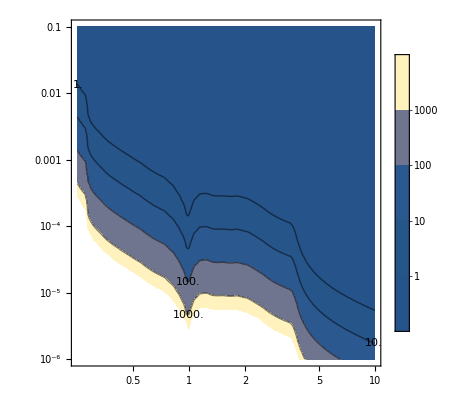

```mathematica
ContourPlot[γβϕB[mϕ]cτϕBRDM[mϕ,α,0] /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,10},{α,10^-6,0.1},PlotLegends->Automatic,ScalingFunctions->{"Log","Log"},ContourLabels->True,Contours->{1,10,100,1000}]
```

InterpolatingFunction::dmval: Input value {0.250066} lies outside the range of data in the interpolating function. Extrapolation will be used.

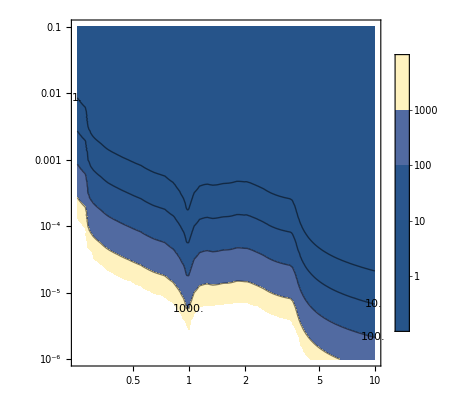

```mathematica
ContourPlot[cτϕBRDM[mϕ,α,0] /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,10},{α,10^-6,0.1},PlotLegends->Automatic,ScalingFunctions->{"Log","Log"},ContourLabels->True,Contours->{1,10,100,1000}]
```

### B -> K μμ width

```mathematica
(* The interesting part about the B->Kμμ - process is in the resonance, so that we can take *)
```

```mathematica
ΓBtoKμμ[mϕ_,mχ_,ξ_,α_]:=ΓBtoKϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/Γϕ[mϕ,mχ,ξ,α]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoKϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoXsμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoXsϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoXsππBRDM[mϕ_,α_,BRχ_]:=ΓBtoXsϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKϕ[mϕ_,α_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fzero[mϕ^2]^2 (mB-mK)^2 (mB+mK)^2 (MB+MS)^2 Sqrt[(mB+mK-mϕ) (mB-mK+mϕ) (mB^2-(mK+mϕ)^2)] (2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2 (MW^2-MT^2)^6)HeavisideTheta[mB-(mK+mϕ)]
```

```mathematica
ΓBtoXsϕ[mϕ_,α_]:=((Sin[α]mb)/vev (3 √2 GF mt^2 Conjugate[Vts]Vtb)/(15 π^2))^2((mB^2-mϕ^2)^2)/(32 π mB^3)
```

```mathematica
BRBtoKμμBRDMKLM[mϕ_,α_,BRχ_]:=GeomIntBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],0,RKLM,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ΓBtoKμμBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BRBtoKμμBRDMCDC[mϕ_,α_,BRχ_]:=GeomIntBelleII[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],0,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ΓBtoKμμBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

#### Checks/plots

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

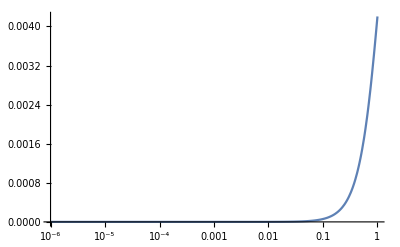

```mathematica
LogLinearPlot[BRBtoKμμBRDMKLM[4,α,0],{α,10^-6,10^0},PlotRange->Full]
```

### B -> K inv width

```mathematica
(* The interesting part about the B->Kμμ - process is in the resonance, so that we can take *)
```

```mathematica
ΓBtoKϕ[mϕ_,α_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fzero[mϕ^2]^2 (mB-mK)^2 (mB+mK)^2 (MB+MS)^2 Sqrt[(mB+mK-mϕ) (mB-mK+mϕ) (mB^2-(mK+mϕ)^2)] (2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2 (MW^2-MT^2)^6)HeavisideTheta[mB-(mK+mϕ)]
```

```mathematica
(*BR(B -> ϕK)*(GeomFactor*BR(ϕ->SM)+BR(ϕ->inv))*)
```

```mathematica
BRBtoϕKLM[mϕ_,α_,BRχ_]:=(GeomIntInvBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],RKLM,cτϕVisible[mϕ,α],γβϕB[mϕ]]ΓϕSM[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]+BRχ) ΓBtoKϕ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BRBtoϕCDC[mϕ_,α_,BRχ_]:=(GeomIntInvBelleII[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],RCDC,cτϕVisible[mϕ,α],γβϕB[mϕ]] ΓϕSM[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]+BRχ)ΓBtoKϕ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

#### Checks/plots

```mathematica
LogLogPlot[BRBtoϕKLM[4,α],{α,10^-6,10^0},PlotRange->Full]
```

-Graphics-

```mathematica
GeomIntInvisible[θKLMMin,θKLMMax,RKLM,cτϕVisible[4,10^-6],γβϕB[4]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::nlim: θ = θKLMMin is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.580416

InterpolatingFunction::dmval: Input value {0.250097} lies outside the range of data in the interpolating function. Extrapolation will be used.

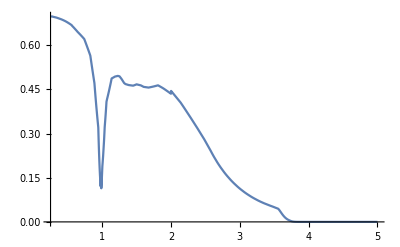

```mathematica
Plot[GeomIntInvBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],RKLM,cτϕVisible[mϕ,10^-5],γβϕB[mϕ]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,5}]
```

General::munfl: Exp[-744.44] is too small to represent as a normalized machine number; precision may be lost.

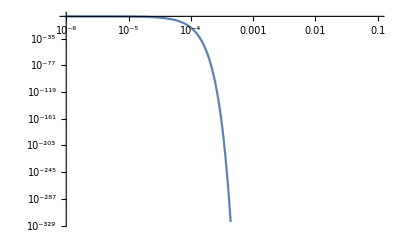

```mathematica
LogLogPlot[GeomIntInvBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],RKLM,cτϕVisible[1.9,α],γβϕB[1.9]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{α,10^-6,10^-1},PlotRange->Full]
```

#### SM contribution

```mathematica
m23.b2plus[q.b2_,mχ_]=m23.b2/.(Solve[q.b2==4 (mχ^2+p1.b2)&&q.b2==mB^2+mK^2-2 Sqrt[mB^2+p3.b2] Sqrt[mK^2+p3.b2]+2 p3.b2&&m23.b2==mK^2+mχ^2+2 Sqrt[mχ^2+p1.b2] Sqrt[mK^2+p3.b2]+2 Sqrt[p1.b2] Sqrt[p3.b2],{p1.b2,p3.b2,m23.b2}]//Simplify//#//.{Sqrt[q.b2] Sqrt[a_/q.b2]:>Sqrt[a],Sqrt[a_^2]:>-a}&)[[1]];
m23.b2minus[q.b2_,mχ_]=m23.b2/.(Solve[q.b2==4 (mχ^2+p1.b2)&&q.b2==mB^2+mK^2-2 Sqrt[mB^2+p3.b2] Sqrt[mK^2+p3.b2]+2 p3.b2&&m23.b2==mK^2+mχ^2+2 Sqrt[mχ^2+p1.b2] Sqrt[mK^2+p3.b2]-2 Sqrt[p1.b2] Sqrt[p3.b2],{p1.b2,p3.b2,m23.b2}]//Simplify//#//.{Sqrt[q.b2] Sqrt[a_/q.b2]:>Sqrt[a],Sqrt[a_^2]:>-a}&)[[1]];
```

```mathematica
dΓdq.b2SMνν[q.b2_]=1/((2 π)^3 32 mB^3)*2*Subscript[α,em]^2/π^2*3 GF^2 Vtb^2 Vts^2 Subscript[X,t]^2/sw.b2^2 (Abs[fplus[q.b2]])^2 Integrate[((mB^2-m23.b2) (m23.b2+q.b2-mK^2)-mB^2 q.b2),{m23.b2,m23.b2minus[q.b2,0],m23.b2plus[q.b2,0]}]//Simplify
```

(GF^2 (q.b2)^(3/2) ((mB^4+(mK^2-q.b2)^2-2 mB^2 (mK^2+q.b2))/(q.b2))^(3/2) Vtb^2 Vts^2 Abs[fplus[q.b2]]^2 X_t^2 α_em^2)/(256 mB^3 π^5 (sw.b2)^2)

```mathematica
ΓSMνν=NIntegrate[dΓdq.b2SMνν[q.b2]/.formFactors/.values/.masses/.ckms/.couplings/.MH:>125,{q.b2,0,(mB-mK)^2/.masses}];
```

```mathematica
BRBtoKννSM=ΓSMνν/ΓtotalB
```

4.01009×10^-6

### B -> K μμ scans

```mathematica
ContourPlot[GeomIntBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],0,RKLM,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]/GeomIntBelleII[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],0,RCDC,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,5},{α,10^-5,10^-1},ContourLabels->True,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},PlotLegends->Automatic]
Export["GeomIntKLM-CDC.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

GeomIntKLM-CDC.png

#### KLM

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

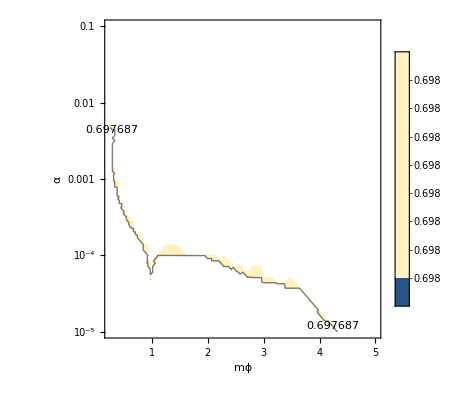

GeomIntKLM.png

```mathematica
ContourPlot[GeomIntBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],0,RKLM,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,5},{α,10^-5,10^-1},ContourLabels->True,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},PlotLegends->Automatic]
Export["GeomIntKLM.png",%]
```

```mathematica
PlotContoursLabeled[BRBtoKμμBRDMKLM,0,0.25,5,10^-5,10^-1,10^-12,10^-3,9,2.5]
Export["BRBtoKmumuKLM_BR0.png",%]
```

{1.×10^-12,1.×10^-11,1.×10^-10,1.×10^-9,1.×10^-8,1.×10^-7,1.×10^-6,0.00001,0.0001,0.001}

{{2.5,1.×10^-2},{2.5,1.×10^-2},{2.5,1.×10^-2},{2.5,1.×10^-2},{2.5,1.×10^-2},{2.5,1.×10^-2},{2.5,1.×10^-2},{2.5,1.×10^-2},{2.5,1.×10^-2},{2.5,1.×10^-2}}

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

BRBtoKmumuKLM_BR0.png

```mathematica
PlotContours[BRBtoKμμBRDMKLM,0.1,0.25,5,10^-5,10^-1,10^-11,10^-3,8]
Export["BRBtoKmumuKLM_BR0.1.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

BRBtoKmumuKLM_BR0.1.png

```mathematica
PlotContours[BRBtoKμμBRDMKLM,0.5,0.25,5,10^-5,10^-1,10^-11,10^-3,8]
Export["BRBtoKmumuKLM_BR0.5.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

BRBtoKmumuKLM_BR0.5.png

```mathematica
PlotContours[BRBtoKμμBRDMKLM,0.9,0.25,5,10^-5,10^-1,10^-11,10^-3,8]
Export["BRBtoKmumuM_BR0.9.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

BRBtoKmumuM_BR0.9.png

#### CDC

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

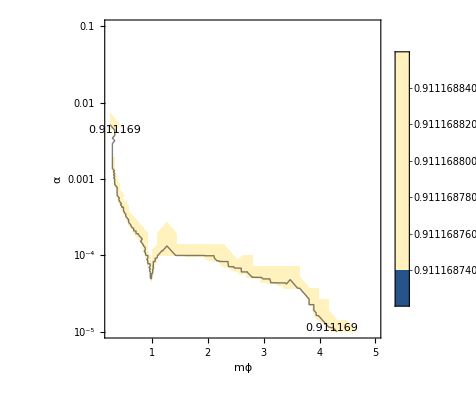

GeomIntCDC.png

```mathematica
ContourPlot[GeomIntBelleII[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],0,RCDC,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,5},{α,10^-5,10^-1},ContourLabels->True,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},PlotLegends->Automatic]
Export["GeomIntCDC.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

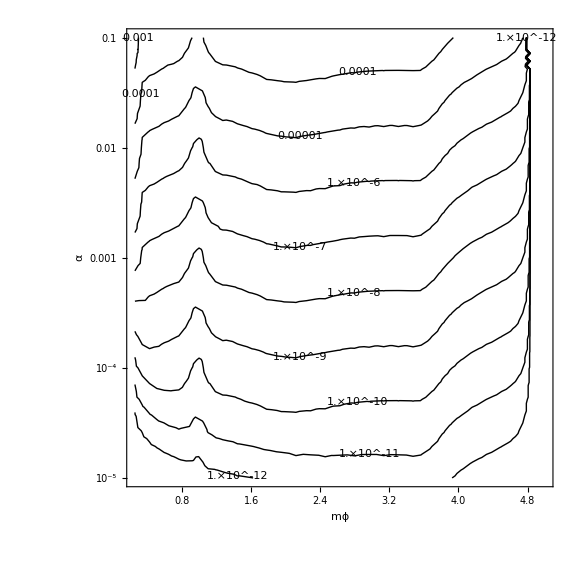

BRBtoKmumuCDC_BR0.png

```mathematica
ContourPlot[BRBtoKμμBRDMCDC[mϕ,α,0],{mϕ,0.25,5},{α,10^-5,10^-1},ContourShading-> None,ContourLabels->All,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},ImageSize->Large,Contours->{10^-12,10^-11,10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,10^-3},ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],Exclusions->None,PlotRange->Full]
Export["BRBtoKmumuCDC_BR0.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

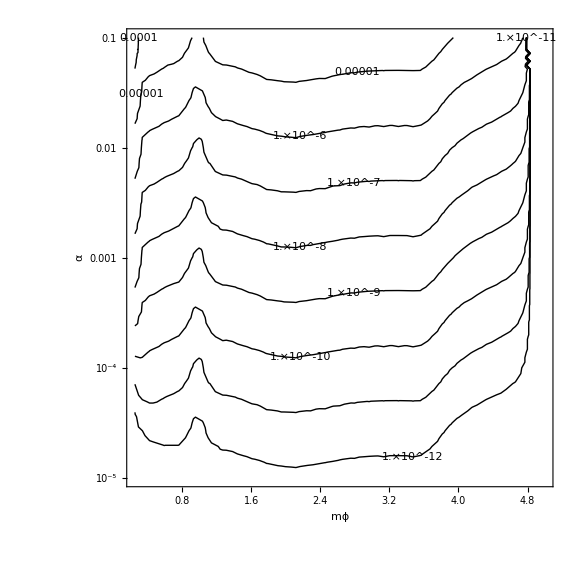

BRBtoKmumuCDC_BR0.9.png

```mathematica
ContourPlot[BRBtoKμμBRDMCDC[mϕ,α,0.9],{mϕ,0.25,5},{α,10^-5,10^-1},ContourShading-> None,ContourLabels->All,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},ImageSize->Large,Contours->{10^-12,10^-11,10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,10^-3},ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],Exclusions->None,PlotRange->Full]
Export["BRBtoKmumuCDC_BR0.9.png",%]
```

### B -> K inv scans

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45733}. NIntegrate obtained 1.2515×10^-319+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.03765}. NIntegrate obtained 3.×10^-323+0. ⅈ and 0. for the integral and error estimates.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.03765}. NIntegrate obtained 5.×10^-324+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

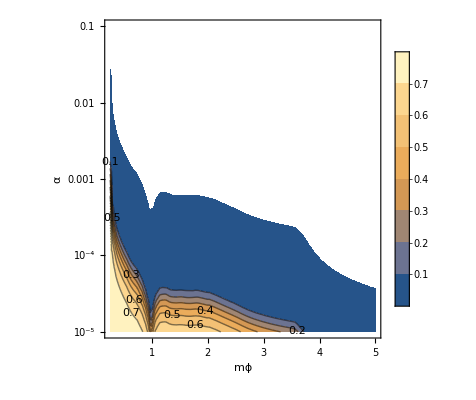

GeomInt_inv_KLM-CDC.png

```mathematica
ContourPlot[GeomIntInvBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],RKLM,cτϕVisible[mϕ,α],γβϕB[mϕ]]/GeomIntInvBelleII[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],RCDC,cτϕVisible[mϕ,α],γβϕB[mϕ]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,5},{α,10^-5,10^-1},ContourLabels->True,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},PlotLegends->Automatic]
Export["GeomInt_inv_KLM-CDC.png",%]
```

#### KLM

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

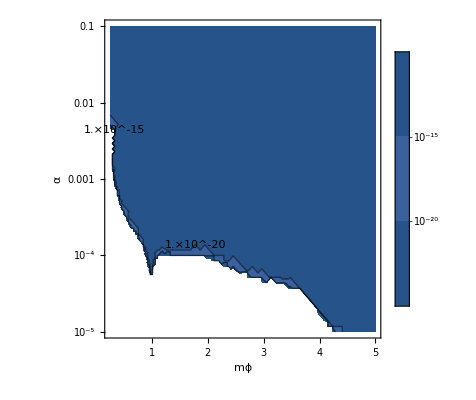

GeomInt_inv_KLM.png

```mathematica
ContourPlot[GeomIntInvBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],RKLM,cτϕVisible[mϕ,α],γβϕB[mϕ]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,5},{α,10^-5,10^-1},ContourLabels->True,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},PlotLegends->Automatic,Contours-> {10^-5,10^-10,10^-15,10^-20}]
Export["GeomInt_inv_KLM.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

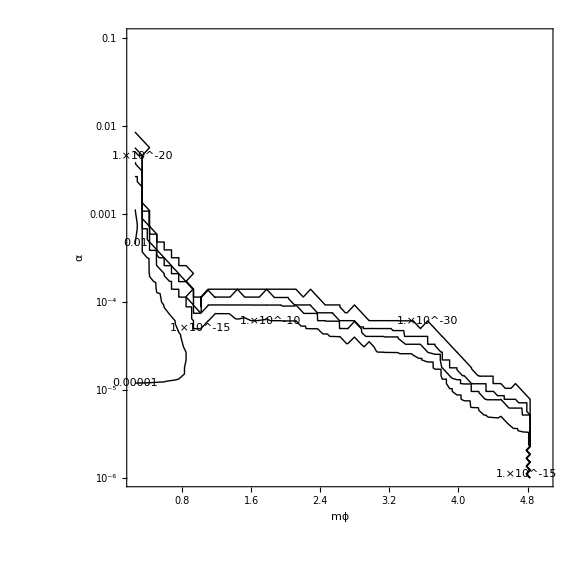

RinvKLM_BR0.png

```mathematica
ContourPlot[BRBtoϕKLM[mϕ,α,0]/BRBtoKννSM,{mϕ,0.25,5},{α,10^-6,10^-1},ContourShading-> None,ContourLabels->All,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},ImageSize->Large,Contours->{10^-30,10^-20,10^-15,10^-10,10^-5,10^-2,10^-1},ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],Exclusions->None,PlotRange->Full]
Export["RinvKLM_BR0.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

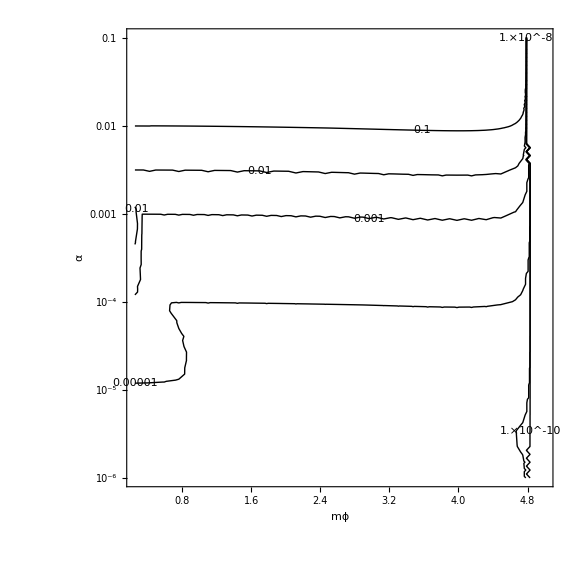

RinvKLM_BR0.01.png

```mathematica
ContourPlot[BRBtoϕKLM[mϕ,α,0.01]/BRBtoKννSM,{mϕ,0.25,5},{α,10^-6,10^-1},ContourShading-> None,ContourLabels->All,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},ImageSize->Large,Contours->{10^-10,10^-8,10^-5,10^-3,10^-2,10^-1},ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],Exclusions->None,PlotRange->Full]
Export["RinvKLM_BR0.01.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

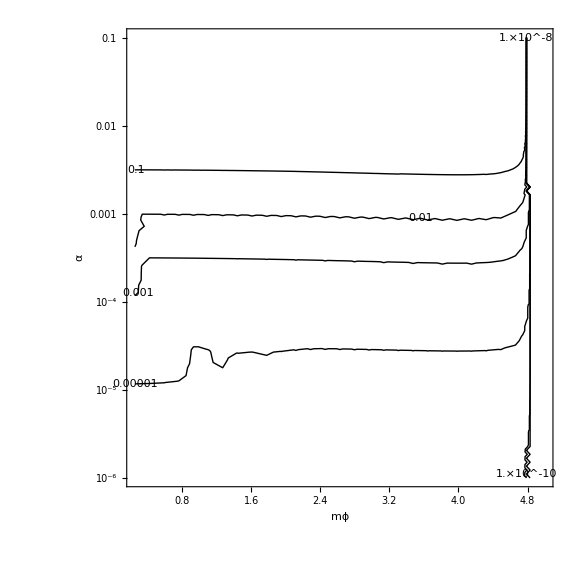

RinvKLM_BR0.1.png

```mathematica
ContourPlot[BRBtoϕKLM[mϕ,α,0.1]/BRBtoKννSM,{mϕ,0.25,5},{α,10^-6,10^-1},ContourShading-> None,ContourLabels->All,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},ImageSize->Large,Contours->{10^-10,10^-8,10^-5,10^-3,10^-2,10^-1},ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],Exclusions->None,PlotRange->Full]
Export["RinvKLM_BR0.1.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

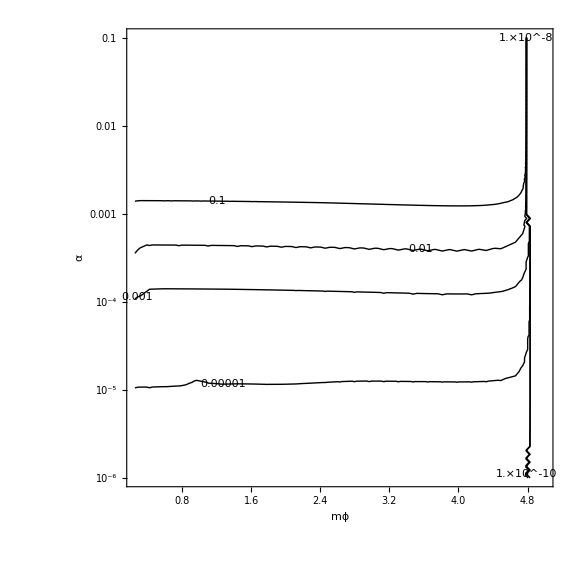

RinvKLM_BR0.5.png

```mathematica
ContourPlot[BRBtoϕKLM[mϕ,α,0.5]/BRBtoKννSM,{mϕ,0.25,5},{α,10^-6,10^-1},ContourShading-> None,ContourLabels->All,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},ImageSize->Large,Contours->{10^-10,10^-8,10^-5,10^-3,10^-2,10^-1},ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],Exclusions->None,PlotRange->Full]
Export["RinvKLM_BR0.5.png",%]
```

#### CDC

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

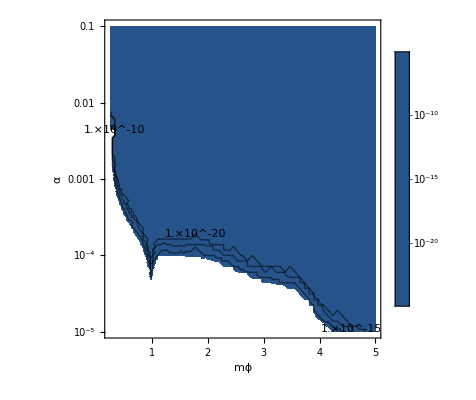

GeomInt_inv_CDC.png

```mathematica
ContourPlot[GeomIntInvBelleII[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],RCDC,cτϕVisible[mϕ,α],γβϕB[mϕ]]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.25,5},{α,10^-5,10^-1},ContourLabels->True,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},PlotLegends->Automatic,Contours-> {10^-5,10^-10,10^-15,10^-20}]
Export["GeomInt_inv_CDC.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

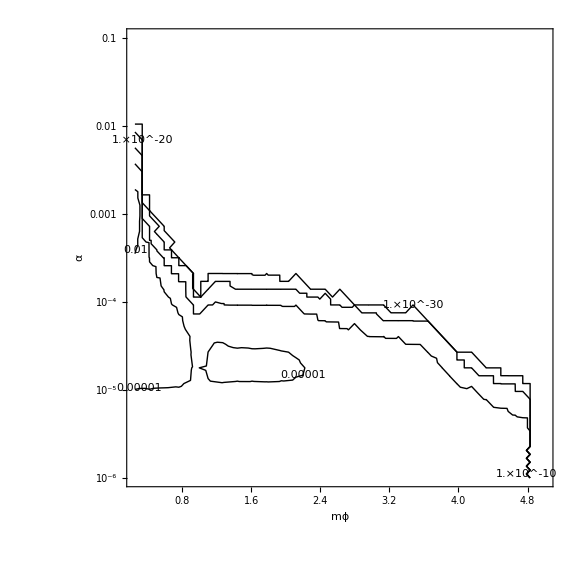

BRBtoKinvCDC_BR0.png

```mathematica
ContourPlot[BRBtoϕCDC[mϕ,α,0]/BRBtoKννSM,{mϕ,0.25,5},{α,10^-6,10^-1},ContourShading-> None,ContourLabels->All,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},ImageSize->Large,Contours->{10^-30,10^-20,10^-10,10^-5,10^-2,10^-1},ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],Exclusions->None,PlotRange->Full]
Export["BRBtoKinvCDC_BR0.png",%]
```

InterpolatingFunction::dmval: Input value {0.250339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

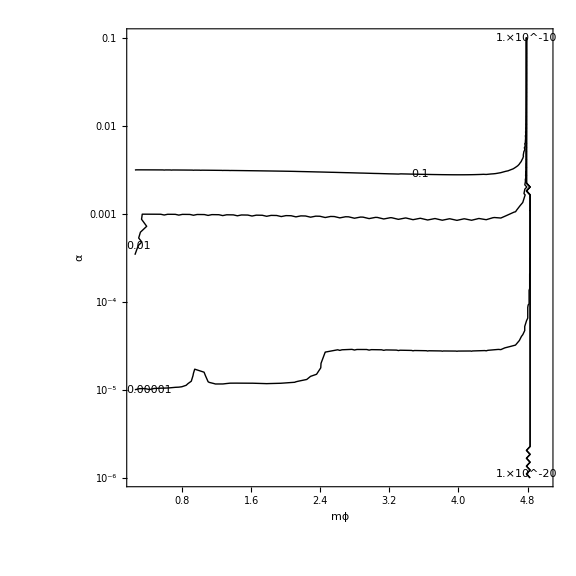

BRBtoKinvCDC_BR0.1.png

```mathematica
ContourPlot[BRBtoϕCDC[mϕ,α,0.1]/BRBtoKννSM,{mϕ,0.25,5},{α,10^-6,10^-1},ContourShading-> None,ContourLabels->All,FrameLabel->{"mϕ","α"},ScalingFunctions->{None,"Log"},ImageSize->Large,Contours->{10^-20,10^-10,10^-5,10^-2,10^-1},ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],Exclusions->None,PlotRange->Full]
Export["BRBtoKinvCDC_BR0.1.png",%]
```